```mathematica
(*ρ[x1_,x2_]:=Sqrt[(x1^2 + x2^2) + γ^2*σ^4 /R^2- 2*γ*σ^2/R*(x1*Cos[ψ] + x2*Sin[ψ])]*)
ClearAll[γ ,R,σ,ψ ];
ρ[x1_,x2_]:=Sqrt[(x1-γ σ^2/R Cos[ψ] )^2 + (x2-γ σ^2/R Sin[ψ])^2 ]
```

### Nulcline plot for uniform density on the ring .

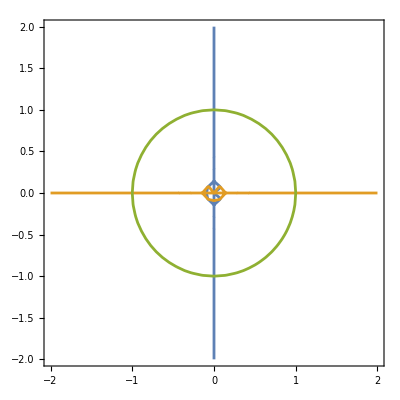

```mathematica
γ = 0;
R = 1;
σ = 0.705;
ψ =2 π/3;
ρ[x1_,x2_]:=Sqrt[(x1-γ σ^2/R Cos[ψ] )^2 + (x2-γ σ^2/R Sin[ψ])^2 ]
ContourPlot[{-x1 + R/ρ[x1,x2] BesselI[1,R/σ^2ρ[x1,x2]]/BesselI[0,R/σ^2ρ[x1,x2]](x1-γ σ^2/R Cos[ψ] )==0,
-x2 + R/ρ[x1,x2] BesselI[1,R/σ^2ρ[x1,x2]]/BesselI[0,R/σ^2ρ[x1,x2]](x2-γ σ^2/R Sin[ψ] )==0,x1^2+x2^2==1},
 {x1,-2.,2.},{x2,-2.,2.}]
```

### Nulcline plot for non uniform density on the ring.

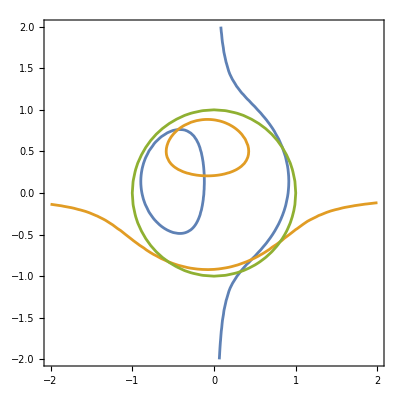

```mathematica
γ = 1;
R = 1;
σ = 0.4;
ψ =2 π/3;
ρ[x1_,x2_]:=Sqrt[(x1-γ σ^2/R Cos[ψ] )^2 + (x2-γ σ^2/R Sin[ψ])^2 ]
ContourPlot[{-x1 + R/ρ[x1,x2] BesselI[1,R/σ^2ρ[x1,x2]]/BesselI[0,R/σ^2ρ[x1,x2]](x1-γ σ^2/R Cos[ψ] )==0,
-x2 + R/ρ[x1,x2] BesselI[1,R/σ^2ρ[x1,x2]]/BesselI[0,R/σ^2ρ[x1,x2]](x2-γ σ^2/R Sin[ψ] )==0,x1^2+x2^2==1},
 {x1,-2.,2.},{x2,-2.,2.}]
```

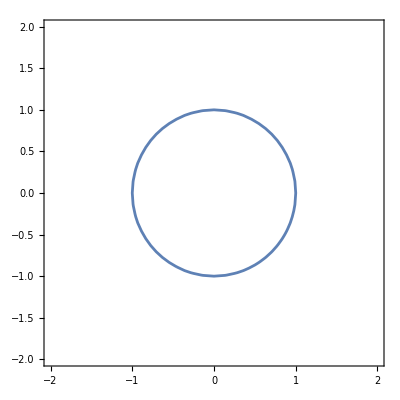
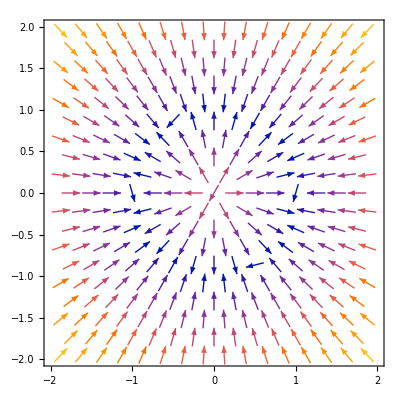

```mathematica
γ = 2;
R = 1;
σ = 0.01;
ψ =1 π/3;
ρ[x1_,x2_]:=Sqrt[(x1-γ σ^2/R Cos[ψ] )^2 + (x2-γ σ^2/R Sin[ψ])^2 ]
SP1 = ContourPlot[{x1^2+x2^2==R ^2},{x1,-2.,2.},{x2,-2.,2.}];
SP2 = VectorPlot[{-x1 + R/ρ[x1,x2] BesselI[1,R/σ^2ρ[x1,x2]]/BesselI[0,R/σ^2ρ[x1,x2]](x1-γ σ^2/R Cos[ψ] ),
-x2 + R/ρ[x1,x2] BesselI[1,R/σ^2ρ[x1,x2]]/BesselI[0,R/σ^2ρ[x1,x2]](x2-γ σ^2/R Sin[ψ] )},
 {x1,-2.,2.},{x2,-2.,2.}];
Overlay[{SP1,SP2}]
```

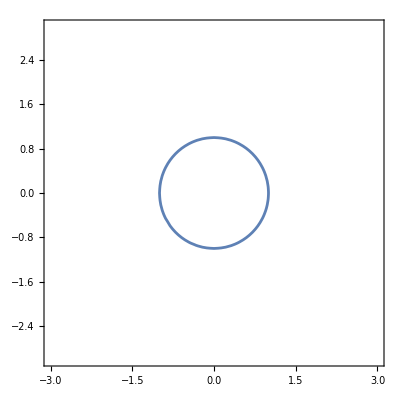

```mathematica
γ = 0;
R = 1;
σ = 0.0001;
ψ = π/4;
ρ[x1_,x2_]:=Sqrt[(x1-γ σ^2/R Cos[ψ] )^2 + (x2-γ σ^2/R Sin[ψ])^2 ]
ContourPlot[ρ[x1,x2] ==1,
 {x1,-3,3},{x2,-3,3}]
```

```mathematica
ContourPlot[x^2+y^2==1, {x,-2,2},{y,-2,2}]
```

-Graphics-

```mathematica
ContourPlot[x^2+y^2==1, {x,-2,2},{y,-2,2}]
```